## Operaciones con listas

En Wolfram Language hay miles de funciones que trabajan con listas.

Puede hacerse aritmética con listas:

```mathematica
{1,2,3}+10
```

{11,12,13}

```mathematica
{1,1,2}*{1,2,3}
```

{1,2,6}

Calcule los 10 primeros cuadrados:

```mathematica
Range[10]^2
```

{1,4,9,16,25,36,49,64,81,100}

Grafique los 20 primeros cuadrados:

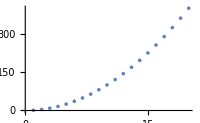

```mathematica
ListPlot[Range[20]^2]
```

Sort ordena una lista:

```mathematica
Sort[{4,2,1,3,6}]
```

{1,2,3,4,6}

Length encuentra la longitud de una lista:

```mathematica
Length[{5,3,4,5,3,4,5}]
```

7

Total calcula la suma de los elementos de una lista:

```mathematica
Total[{1,1,2,2}]
```

6

Encuentre el total de los números del 1 al 10:

```mathematica
Total[Range[10]]
```

55

Count cuenta el número de veces que alguna cosa aparece en una lista.

Cuente el número de veces que a aparece en la lista:

```mathematica
Count[{a,b,a,a,c,b,a},a]
```

4

Frecuentemente es de utilidad obtener elementos individuales de una lista. First encuentra el primer elemento; Last encuentra el último. Part encuentra el elemento que está en una posición especificada.

Obtenga el primer elemento de una lista:

```mathematica
First[{7,6,5}]
```

7

Obtenga el último elemento:

```mathematica
Last[{7,6,5}]
```

5

Obtenga el elemento número 2:

```mathematica
Part[{7,6,5},2]
```

6

Obtener el primer elemento de una lista previamente ordenada es lo mismo que obtener el elemento más pequeño:

```mathematica
First[Sort[{6,7,1,2,4,5}]]
```

1

```mathematica
Min[{6,7,1,2,4,5}]
```

1

Si se tiene un número, como el 5671, puede obtenerse la lista de sus dígitos mediante IntegerDigits[5671].

Descomponga un número para obtener la lista de sus dígitos:

```mathematica
IntegerDigits[1988]
```

{1,9,8,8}

Encuentre el último dígito:

```mathematica
Last[IntegerDigits[1988]]
```

8

Take permite tomar un número especificado de elementos a partir del principio de una lista.

Tome los 3 primeros elementos de una lista:

```mathematica
Take[{101,203,401,602,332,412},3]
```

{101,203,401}

Tome los 10 primeros dígitos de 2 a la potencia 100:

```mathematica
Take[IntegerDigits[2^100],10]
```

{1,2,6,7,6,5,0,6,0,0}

Drop desecha elementos a partir del inicio de una lista.

```mathematica
Drop[{101,203,401,602,332,412},3]
```

{602,332,412}

Vocabulario

{2,3,4}+{5,6,2} |   | aritmética con listas
Sort[{5,7,1}] |   | ordena una lista
Length[{3,3}] |   | longitud de una lista (número de elementos)
Total[{1,1,2}] |   | total de los elementos de una lista
Count[{3,2,3},3] |   | cuenta cuántas veces aparece un elemento
First[{2,3}] |   | primer elemento de una lista
Last[{6,7,8}] |   | último elemento de una lista
Part[{3,1,4},2] |   | un elemento particular de una lista, que también se escribe como {3,1,4}[[2]]
Take[{6,4,3,1},2] |   | toma elementos del principio de la lista
Drop[{6,4,3,1},2] |   | desecha elementos del principio de una lista
IntegerDigits[1234] |   | lista de los dígitos de un número

"14 Exercises Available"
"with 7 extras" | "Get Started »"

Cree una lista de los 10 primeros cuadrados en orden inverso. »

| Expected output: |  
  | {100,81,64,49,36,25,16,9,4,1} |

Calcule el total de los 10 primeros cuadrados. »

| Expected output: |  
  | 385 |

Muestre gráficamente los 10 primeros cuadrados, comenzando por el 1. »

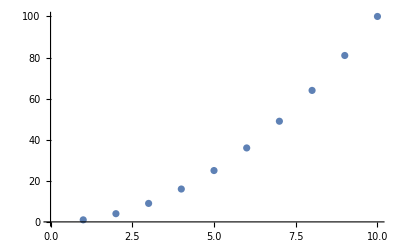
| Expected output: |  
  | -Graphics- |

Use Sort, Join y Range para crear {1,1,2,2,3,3,4,4}. »

| Expected output: |  
  | {1,1,2,2,3,3,4,4} |

Use Range y + para formar la lista de los números del 10 al 20, inclusive. »

| Expected output: |  
  | {10,11,12,13,14,15,16,17,18,19,20} |

Forme una lista combinada de los 5 primeros cuadrados y cubos (números elevados a la potencia 3), puestos en orden. »

| Expected output: |  
  | {1,1,4,8,9,16,25,27,64,125} |

Encuentre el número de dígitos en 2^128. »

| Expected output: |  
  | 39 |

Encuentre el primer dígito de 2^32. »

| Expected output: |  
  | 4 |

Encuentre los 10 primeros dígitos en 2^100. »

| Expected output: |  
  | {1,2,6,7,6,5,0,6,0,0} |

Encuentre el mayor de los dígitos en 2^20. »

| Expected output: |  
  | 8 |

Encuentre cuántos ceros hay en los dígitos de 2^1000. »

| Expected output: |  
  | 28 |

Use Part, Sort e IntegerDigits para encontrar el segundo menor de los dígitos en 2^20. »

| Expected output: |  
  | 1 |

Represente gráficamente los puntos unidos de la secuencia de dígitos que aparecen en 2^128. »

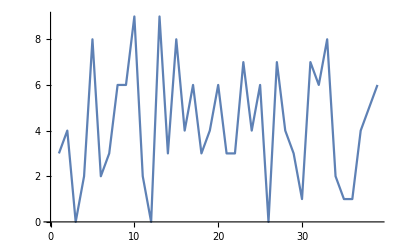
| Expected output: |  
  | -Graphics- |

Use Take y Drop para obtener la secuencia 11 al 20 en Range[100]. »

| Expected output: |  
  | {11,12,13,14,15,16,17,18,19,20} |

Cree una lista de los 10 primeros múltiplos de 3. »

| Expected output: |  
  | {3,6,9,12,15,18,21,24,27,30} |

Forme la lista de los 10 primeros cuadrados, usando únicamente Range y Times. »

| Expected output: |  
  | {1,4,9,16,25,36,49,64,81,100} |

Encuentre el último dígito de 2^37. »

| Expected output: |  
  | 2 |

Encuentre el penúltimo dígito de 2^32. »

| Expected output: |  
  | 9 |

Encuentre la suma de todos los dígitos en 3^126. »

| Expected output: |  
  | 234 |

Construya el diagrama circular de la secuencia de los dígitos que aparecen en 2^32. »

| Expected output: |  
  | -Graphics- |

Haga una lista de diagramas circulares para las secuencias de los dígitos que aparecen en 2^20, 2^40, 2^60. »

| Expected output: |  
  | {-Graphics-,-Graphics-,-Graphics-} |

Preguntas y respuestas

¿Pueden sumarse listas de diferente longitud?

No. {1,2}+{1,2,3} no funciona. {1,2,0}+{1,2,3} está bien si, en efecto, eso es lo que se quiere.

¿Puede haber una lista que no contenga nada?

Sí. {} es una lista de longitud cero, sin elementos. Generalmente se le llama lista nula o lista vacía.

Notas técnicas

IntegerDigits[5671] da los dígitos en base 10. IntegerDigits[5671,2] da los dígitos en base 2. Puede usarse cualquier base. FromDigits[{5,6,7,1}] reconstruye un número a partir de la lista de sus dígitos.

Rest[lista] da todos los elementos de lista excepto el primero. Most[lista] da todos los elementos excepto el último.

Para explorar más

Guía para manipulación de listas en Wolfram Language »